```mathematica
Clear["Global`*"];
rep={Γs->645 10^-6,Γr->3457 10^-6,Γe->35.9,Ωc->10,Δs->0,Δp->0};
k1=Tuples[{0,1},3];
Lengthscale=Length[scaleList];
Table[{
resultsList=Table[{},{i,20}];
k=k1⟦folderid⟧;
path=StringJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],StringReplace["\\data\\resolution\\resolution\\γ",{"γ"->StringJoin[{ToString[k⟦1⟧],ToString[k⟦2⟧],ToString[k[[3]]]}]}]}];
SetDirectory[path];
Table[{
data1=Import[StringJoin[path, ToString[StringForm["\\``",FileNames[]⟦id⟧ ]]],"TSV"];
DATA1=Table[data1[[i,j]],{i,2,Length[data1]},{j,{1,3}}];
DATA1⟦All,2⟧=(DATA1⟦All,2⟧-Min[DATA1⟦All,2⟧])/(Max[DATA1⟦All,2⟧]-Min[DATA1⟦All,2⟧]);
Data1=Table[0,{i,1,Length[DATA1]},{j,1,2}];

For[i=1,i<Length[DATA1]+1,i++,
{Data1[[i,1]]=(DATA1[[i,1]])*100000,
Data1[[i,2]]=DATA1[[i,2]]}];
Ec=A1 Cos[w1*t+α5]+A2 Cos[w2*t+α4]+A3 Cos[w3*t+α3]+A4 Cos[w4*t+α2];
Es=-(A1 Sin[w1*t+α5]+A2 Sin[w2*t+α4]+A3 Sin[w3*t+α3]+A4 Sin[w4*t+α2]);
A1=A2=A3=1;A4=10;
w1=1*12.56;w2=2*12.56;w3=3*12.56;w4=4*12.56;

Ωs=Ae √(Ec^2+Es^2);

α2=0;

ρeg[Γr_,t_,Γs_,Γe_,Ωc_,Δc_]:=(Γs (-Γs/2-ⅈ (Δc+Δp+Δs)) Ωc ((ⅈ (Γr+2 ⅈ Δc+2 ⅈ Δp))/Ωc+(ⅈ Ωs^2)/((Γs+2 ⅈ Δc+2 ⅈ Δp+2 ⅈ Δs) Ωc)))/(4 ((-Γs/2-ⅈ (Δc+Δp+Δs)) (Γs (-Γe/2-ⅈ Δp) (-Γr/2-ⅈ (Δc+Δp))+(Γs Ωc^2)/4)+1/4 Γs (-Γe/2-ⅈ Δp) Ωs^2));

TT[A_,B_,Γr_,t_,Ae_,α3_,α4_,α5_,Γs_,Γe_,Ωc_,Δc_]=A(Exp[Im[-ρeg[Γr ,t,Γs,Γe,Ωc,Δc]]]-B);

aa=FindFit[Data1,{TT[A,B,Γr,t-t0,Ae,α3,α4,α5,Γs,Γe,Ωc,Δc]/.rep,-Pi<=α3<=0,-Pi<=α4<=0,-Pi<=α5<=0,-0.01≤t0<=0.01,Ae>0},{α3,α4,α5,Δc,{A,25},B,{t0,0},Ae},t];

bb=Table[{t,TT[A,B,Γr,t-t0,Ae,α3,α4,α5,Γs,Γe,Ωc,Δc]/.aa/.rep},{t,0,1,0.0002}];


resultsList⟦id⟧=Flatten[{-Round[(α5/.aa)/Pi]*4-Round[(α4/.aa)/Pi]*2-Round[(α3/.aa)/Pi]}];



(*ListPlot[{Data1,bb},FrameLabel->{" Time (ms)","Transmission (a.u.)"},PlotRange->All,Joined->{False,True},Frame->True,PlotStyle->{{Black,PointSize[0.008]},{Red,Thickness[0.01]}},AspectRatio->0.5,LabelStyle->{FontSize->22,FontFamily->"Times",,Black},PlotLabel->StringForm["Tru=``, pred=``",folderid-1,results]]*)
},{id,1,20}]
;Print[resultsList]
},{folderid,1,8}]
```

{{0},{0},{0},{4},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{4},{0}}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindFit::cvmit will be suppressed during this calculation.

{{0},{1},{0},{1},{1},{1},{1},{1},{1},{1},{1},{1},{0},{0},{1},{5},{1},{1},{1},{1}}

{{6},{2},{2},{2},{2},{2},{1},{4},{4},{2},{2},{2},{2},{4},{2},{4},{2},{2},{2},{2}}

{{7},{7},{3},{7},{7},{0},{3},{7},{0},{3},{3},{7},{3},{3},{3},{7},{3},{3},{3},{3}}

{{0},{4},{0},{0},{4},{4},{4},{4},{0},{4},{4},{0},{0},{4},{4},{4},{4},{4},{4},{4}}

{{0},{5},{5},{1},{1},{0},{1},{1},{1},{1},{5},{3},{0},{0},{0},{0},{3},{1},{0},{5}}

{{6},{6},{0},{0},{6},{6},{0},{6},{0},{6},{4},{6},{2},{6},{6},{6},{0},{6},{6},{7}}

{{3},{7},{0},{7},{7},{0},{6},{7},{7},{3},{0},{0},{0},{0},{7},{2},{7},{1},{7},{0}}

{{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null}}

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindFit::cvmit will be suppressed during this calculation.

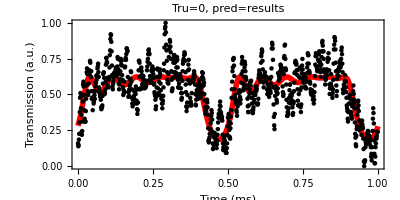
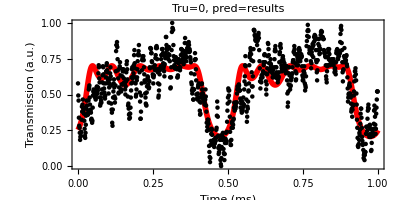
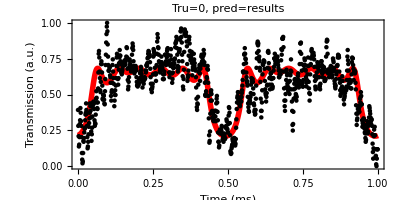
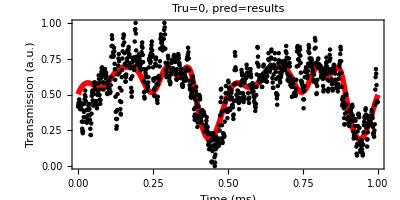
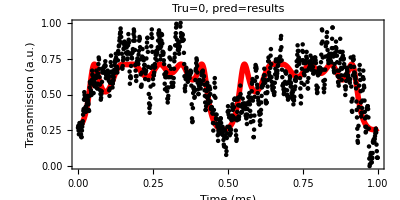
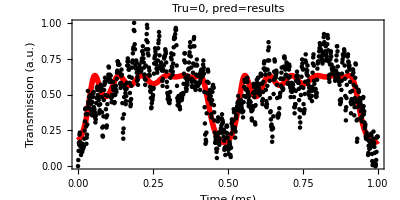
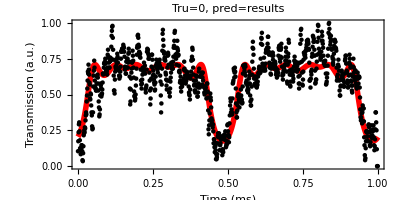
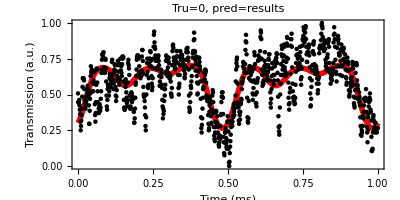
{{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}},{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}},{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}},{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}},{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}},{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}},{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}},{{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}}}

```mathematica
Clear["Global`*"];
rep={Γs->645 10^-6,Γr->3457 10^-6,Γe->35.9,Ωc->10,Δs->0,Δp->0};
k1=Tuples[{0,1},3];
Lengthscale=Length[scaleList];
Table[{
resultsList=Table[{},{i,20}];
k=k1⟦folderid⟧;
path=StringJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],StringReplace["\\data\\resolution\\resolution\\γ",{"γ"->StringJoin[{ToString[k⟦1⟧],ToString[k⟦2⟧],ToString[k[[3]]]}]}]}];
SetDirectory[path];
Table[{
data1=Import[StringJoin[path, ToString[StringForm["\\``",FileNames[]⟦id⟧ ]]],"TSV"];
DATA1=Table[data1[[i,j]],{i,2,Length[data1]},{j,{1,3}}];
DATA1⟦All,2⟧=(DATA1⟦All,2⟧-Min[DATA1⟦All,2⟧])/(Max[DATA1⟦All,2⟧]-Min[DATA1⟦All,2⟧]);
Data1=Table[0,{i,1,Length[DATA1]},{j,1,2}];

For[i=1,i<Length[DATA1]+1,i++,
{Data1[[i,1]]=(DATA1[[i,1]])*100000,
Data1[[i,2]]=DATA1[[i,2]]}];
Ec=A1 Cos[w1*t+α5]+A2 Cos[w2*t+α4]+A3 Cos[w3*t+α3]+A4 Cos[w4*t+α2];
Es=-(A1 Sin[w1*t+α5]+A2 Sin[w2*t+α4]+A3 Sin[w3*t+α3]+A4 Sin[w4*t+α2]);
A1=A2=A3=1;A4=10;
w1=1*12.56;w2=2*12.56;w3=3*12.56;w4=4*12.56;

Ωs=Ae √(Ec^2+Es^2);

α2=0;

ρeg[Γr_,t_,Γs_,Γe_,Ωc_,Δc_]:=(Γs (-Γs/2-ⅈ (Δc+Δp+Δs)) Ωc ((ⅈ (Γr+2 ⅈ Δc+2 ⅈ Δp))/Ωc+(ⅈ Ωs^2)/((Γs+2 ⅈ Δc+2 ⅈ Δp+2 ⅈ Δs) Ωc)))/(4 ((-Γs/2-ⅈ (Δc+Δp+Δs)) (Γs (-Γe/2-ⅈ Δp) (-Γr/2-ⅈ (Δc+Δp))+(Γs Ωc^2)/4)+1/4 Γs (-Γe/2-ⅈ Δp) Ωs^2));

TT[A_,B_,Γr_,t_,Ae_,α3_,α4_,α5_,Γs_,Γe_,Ωc_,Δc_]=A(Exp[Im[-ρeg[Γr ,t,Γs,Γe,Ωc,Δc]]]-B);

aa=FindFit[Data1,{TT[A,B,Γr,t-t0,Ae,α3,α4,α5,Γs,Γe,Ωc,Δc]/.rep,-Pi<=α3<=0,-Pi<=α4<=0,-Pi<=α5<=0,-0.01≤t0<=0.01,Ae>0},{α3,α4,α5,Δc,{A,25},B,{t0,0},Ae},t];

bb=Table[{t,TT[A,B,Γr,t-t0,Ae,α3,α4,α5,Γs,Γe,Ωc,Δc]/.aa/.rep},{t,0,1,0.0002}];


resultsList⟦id⟧={-Round[(α5/.aa)/Pi]*4-Round[(α4/.aa)/Pi]*2-Round[(α3/.aa)/Pi]};

ListPlot[{Data1,bb},FrameLabel->{" Time (ms)","Transmission (a.u.)"},PlotRange->All,Joined->{False,True},Frame->True,PlotStyle->{{Black,PointSize[0.008]},{Red,Thickness[0.01]}},AspectRatio->0.5,LabelStyle->{FontSize->22,FontFamily->"Times",,Black},PlotLabel->StringForm["Tru=``, pred=``",folderid-1,results]]
},{id,1,20}]

},{folderid,1,8}]
```